## Extracting info from 1904.07265

### Data

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Transformation function

```mathematica
Clear[f]
f[Ere_,Etrue_]:=(*1/σe*)Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}]
```

```mathematica
dataN=Table[Maximize[f[i*.5,x],x][[2,1,2]],{i,40}]
```

{1.11111,2.22222,3.33333,4.44444,5.55555,6.66667,7.77777,8.88889,10.,11.111,12.2213,13.3333,14.4444,15.5551,16.6647,17.7778,18.8888,19.9998,21.1102,22.2222,23.3267,24.4444,25.5555,26.6667,27.7769,28.8868,29.9955,31.1022,32.2059,33.3333,34.4444,35.5556,36.6667,37.7778,38.8889,39.994,41.101,42.2222,43.3082,44.4444}

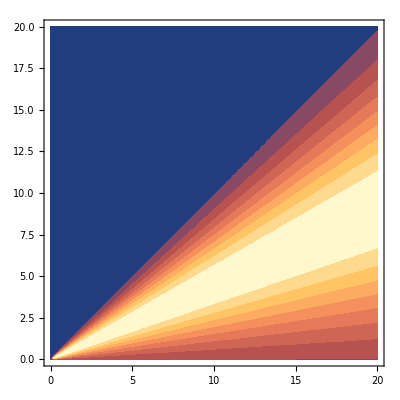

```mathematica
ContourPlot[f[ere,etrue],{etrue,0,20},{ere,0,20},ContourLines->False]//Quiet
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

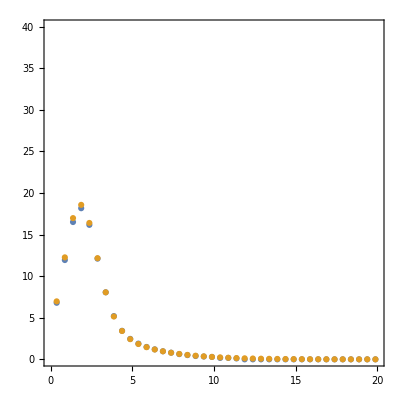

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### Introducing NSI

```mathematica
(* choosing Subscript[ϵ, μτ] only real *)
```

```mathematica
ratio[epS_,ee_]=((0.-2.071438884858977*^-14 ⅈ) epS^2+ee (2.2653175803535897+epS (5.00304469163197+1395.2557007533464 epS))+ee (-2.265317580353589+epS (-19.526840044078167+1355.0510632194855 epS)) Cos[8.323065282815573/ee]+(-0.35192581872734024+epS (-3.159422407231153+256.5539218522311 epS)) Sin[8.323065282815573/ee])/(2.2653175803535897 ee-2.2653175803535897 ee Cos[8.323065282815573/ee]+1.1102230246251565*^-16 ee Cos[16.646130565631147/ee]-0.3519258187273404 Sin[8.323065282815573/ee]);
```

### Plot NSI

```mathematica
(*limite on Subscript[ϵ̃, 23] : 0.08 from my paper with JS *)
(* Subscript[ϵ̃, 23] = Subscript[p, μ] Subscript[ϵ, 23] = 27 Subscript[ϵ, 23] *)
```

```mathematica
Solve[0.08==x*27,x]
```

{{x→0.00296296}}

```mathematica
nsi=0.003;
nsi2=nsi*10;
nsi3=nsi*100;
```

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

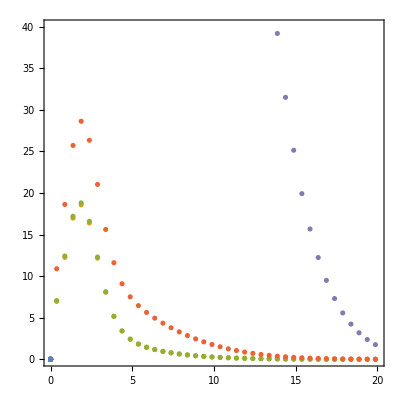

```mathematica
dataNSI=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI2=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi2,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI3=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi3,.5*i],{i,40}]},{j,40}]//Quiet;
ListPlot[{data*0,dataT,dataNSI,dataNSI2,dataNSI3},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

```mathematica
Transpose[{dataT[[All,2]],dataNSI[[All,2]]}]//Chop
```

{{6.97108,7.05987},{12.2612,12.4222},{16.9807,17.2044},{18.5749,18.815},{16.398,16.6002},{12.1658,12.3021},{8.06067,8.13544},{5.15012,5.18276},{3.41041,3.41917},{2.42756,2.42411},{1.84576,1.8363},{1.46299,1.45066},{1.18441,1.17087},{0.968088,0.954282},{0.794312,0.780836},{0.65239,0.63962},{0.535537,0.523702},{0.438937,0.428165},{0.358948,0.349291},{0.292705,0.284162},{0.237899,0.230432},{0.192641,0.186185},{0.155364,0.149839},{0.124757,0.120074},{0.0997192,0.0957867},{0.0793215,0.0760483},{0.0627787,0.0600775},{0.0494268,0.0472163},{0.0387054,0.0369113},{0.0301422,0.0286977},{0.0233408,0.0221871},{0.0179696,0.0170554},{0.0137529,0.0130341},{0.0104624,0.00990164},{0.00791051,0.00747644},{0.00594381,0.00561041},{0.00443777,0.00418368},{0.00329194,0.00309981},{0.00242592,0.00228177},{0.00177576,0.00166847}}

```mathematica
(* checking if it is needed to integrate probability over bin *)
```

```mathematica
Table[{NIntegrate[ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi,.5*i]//Chop,ratio[nsi,.5*i]/NIntegrate[ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi2,.5*i]//Chop,ratio[nsi2,.5*i]/NIntegrate[ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi3,.5*i]//Chop,ratio[nsi3,.5*i]/NIntegrate[ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
```

{{0.979537,1.01595,1.03718},{0.946558,1.01416,1.07142},{0.940641,0.995067,1.05786},{1.0106,1.01525,1.00459},{1.01597,1.01631,1.00033},{1.01627,1.01614,0.999869},{1.01588,1.01557,0.999696},{1.01518,1.01477,0.99959},{1.01429,1.01379,0.999506},{1.01324,1.01266,0.999432},{1.01204,1.01139,0.999362},{1.0107,1.00999,0.999295},{1.00923,1.00845,0.999229},{1.00763,1.00679,0.999163},{1.0059,1.005,0.999098},{1.00405,1.00308,0.999033},{1.00206,1.00103,0.998968},{0.999955,0.998858,0.998903},{0.99772,0.99656,0.998838},{0.995358,0.994136,0.998772},{0.992872,0.991587,0.998706},{0.99026,0.988913,0.998639},{0.987523,0.986113,0.998572},{0.984661,0.983189,0.998504},{0.981674,0.980139,0.998436},{0.978563,0.976965,0.998367},{0.975326,0.973666,0.998298},{0.971965,0.970242,0.998228},{0.968478,0.966694,0.998157},{0.964867,0.96302,0.998086},{0.961132,0.959222,0.998013},{0.957271,0.955299,0.99794},{0.953286,0.951252,0.997866},{0.949176,0.94708,0.997791},{0.944942,0.942783,0.997715},{0.940583,0.938362,0.997639},{0.936099,0.933816,0.997561},{0.931491,0.929145,0.997482},{0.926758,0.92435,0.997402},{0.9219,0.91943,0.99732}}

{{-0.10126+2.42574×10^-17 ⅈ,1.19451,-11.7964},{8.73052,1.41699,0.162303},{7.65834,3.44895,0.450353},{1.77883,1.28218,0.720801},{1.20567,1.17114,0.971357},{1.17623,1.1915,1.01299},{1.22048,1.2544,1.0278},{1.2964,1.34185,1.03505},{1.3935,1.44802,1.03913},{1.50798,1.57054,1.04149},{1.63816,1.70825,1.04279},{1.7832,1.86054,1.04337},{1.94262,2.02705,1.04346},{2.11615,2.20757,1.0432},{2.30361,2.40194,1.04269},{2.50487,2.61009,1.042},{2.71987,2.83193,1.0412},{2.94855,3.06744,1.04032},{3.19087,3.31657,1.03939},{3.4468,3.57929,1.03844},{3.71631,3.8556,1.03748},{3.9994,4.14546,1.03652},{4.29605,4.44889,1.03558},{4.60624,4.76586,1.03465},{4.92998,5.09636,1.03375},{5.26725,5.4404,1.03287},{5.61805,5.79796,1.03202},{5.98238,6.16905,1.0312},{6.36023,6.55366,1.03041},{6.75159,6.95178,1.02965},{7.15648,7.36343,1.02892},{7.57488,7.78858,1.02821},{8.00679,8.22725,1.02753},{8.45221,8.67943,1.02688},{8.91115,9.14512,1.02626},{9.38359,9.62431,1.02565},{9.86954,10.117,1.02507},{10.369,10.6232,1.02452},{10.882,11.143,1.02398},{11.4084,11.6762,1.02347}}

{{-135.543+6.21056×10^-15 ⅈ,6.44436,-0.0475446},{904.799,32.7059,0.0361472},{776.84,275.318,0.354407},{76.0683,16.794,0.220776},{7.64924,3.51552,0.459591},{4.11283,5.92645,1.44097},{9.37644,13.417,1.43092},{18.4215,23.8368,1.29397},{29.9935,36.4923,1.21667},{43.6394,51.0973,1.1709},{59.1585,67.5144,1.14124},{76.4494,85.6699,1.12061},{95.4555,105.521,1.10545},{116.144,127.042,1.09384},{138.492,150.217,1.08466},{162.488,175.032,1.0772},{188.121,201.482,1.07102},{215.386,229.56,1.06581},{244.276,259.262,1.06135},{274.789,290.586,1.05749},{306.922,323.529,1.05411},{340.674,358.089,1.05112},{376.042,394.264,1.04846},{413.025,432.055,1.04607},{451.623,471.46,1.04392},{491.835,512.479,1.04197},{533.66,555.11,1.04019},{577.097,599.353,1.03857},{622.147,645.209,1.03707},{668.808,692.676,1.03569},{717.081,741.755,1.03441},{766.965,792.445,1.03322},{818.461,844.746,1.03211},{871.567,898.657,1.03108},{926.284,954.18,1.03012},{982.612,1011.31,1.02921},{1040.55,1070.06,1.02836},{1100.1,1130.41,1.02755},{1161.26,1192.37,1.0268},{1224.03,1255.95,1.02608}}

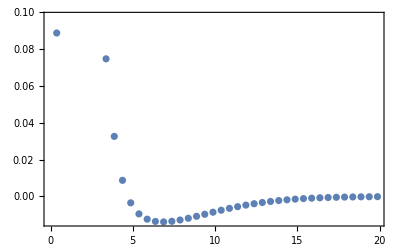

```mathematica
ListPlot[Transpose@{dataT[[All,1]],-dataT[[All,2]]+dataNSI[[All,2]]},Frame->True]
```

```mathematica
Manipulate[Plot[ratio[eps,ee],{ee,.5,20},Frame->True],{eps,0,10^-1}]
```

### Checks

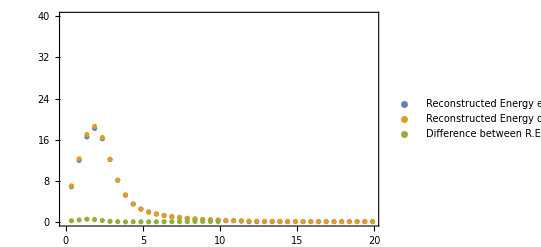

```mathematica
ListPlot[{data,dataT,Transpose[{data[[1;;20,1]],(dataT[[1;;20,2]]-data[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy extracted from figure","Reconstructed Energy obtained internally","Difference between R.E. obtained internally and extracted from figure"},PlotRange->{All,range}]
```

The NSI modulus is 0.003

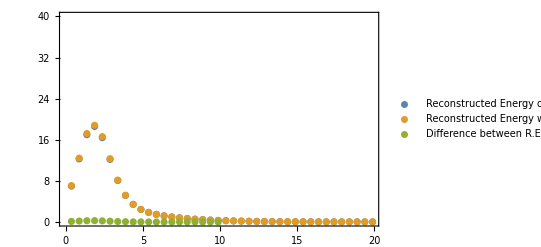

```mathematica
Print["The NSI modulus is ",nsi];ListPlot[{dataT,dataNSI,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,range}]
```

The NSI modulus is 0.03

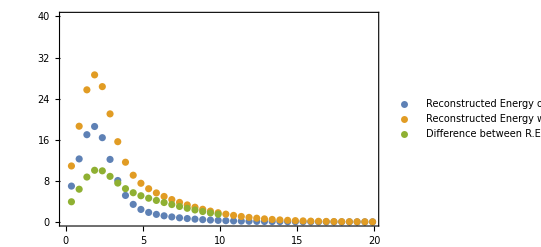

```mathematica
Print["The NSI modulus is ",nsi2];ListPlot[{dataT,dataNSI2,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI2[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,range}]
```

The NSI modulus is 0.3

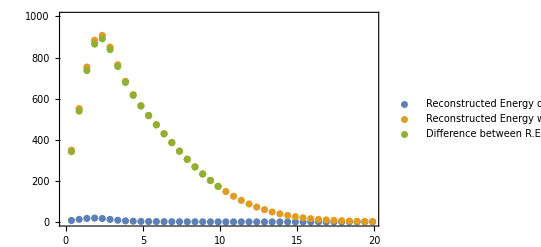

```mathematica
Print["The NSI modulus is ",nsi3];ListPlot[{dataT,dataNSI3,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI3[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,{0,1000}}]
```

### General Probabilitly ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=((-216.76474087618823 ee epS s23 √(1-s23^2)+443.9401382610098 ee epS s23^3 √(1-s23^2)+ee epS (14.523795352446145-17.213387084380614 s23^4) Cos[8.323065282815573/ee-1. δ]-0.555354424129466 ee s23 √(1-s23^2) Cos[δ]+550.8283867001796 ee epS^2 s23^3 √(1-s23^2) Cos[δ]+ee Cos[8.323065282815573/ee] (-8.221113671500182 s23^2+8.221113671500182 s23^4-443.9401382610098 epS √(1-s23^2) (-0.48827470686767177 s23+1. s23^3)+epS^2 (140.54386286655085+5852.64800365708 s23^2-5993.191866523632 s23^4)+550.8283867001796 (0.0010082167831915855+1. epS^2) s23 √(1-s23^2) Cos[δ])+ee epS (2996.595933261816 epS-0.4707740990494358 Cos[8.323065282815573/ee+δ])+39.05849915585865 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-78.1169983117173 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+s23^4 (ee (-8.221113671500182+5993.191866523632 epS^2)+34.42677416876123 ee epS Cos[8.323065282815573/ee+δ]+(1.4466110798466165-1054.5794772081836 epS^2) Sin[8.323065282815573/ee])+s23^2 (ee (8.221113671500182-5852.64800365708 epS^2)+34.42677416876123 ee epS Cos[δ]+(-1.446611079846616+1054.5794772081833 epS^2) Sin[8.323065282815573/ee])-0.5553544241294658 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ])/(2.2653175803535897 ee-2.2653175803535897 ee Cos[8.323065282815573/ee]+1.1102230246251565*^-16 ee Cos[16.646130565631147/ee]-0.3519258187273404 Sin[8.323065282815573/ee]))/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passo=.4/10;
dataGen={};dataGenNSI={};dataGenNSI2={};dataGenNSIp={};dataGenNSI2p={};ls23={};
Do[ss23=(0.582)-.2+passo*i;delta=-2.5;AppendTo[ls23,ss23];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,nsi,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI2,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,nsi2,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSIp,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,-nsi,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI2p,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,-nsi2,.5*i],{i,40}]},{j,40}]],{i,0,10}];
```

0.003

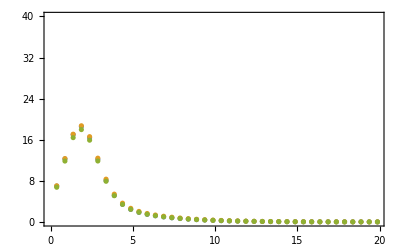
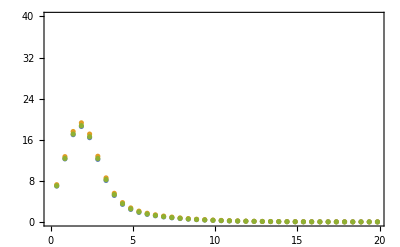
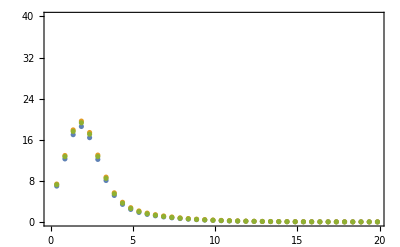
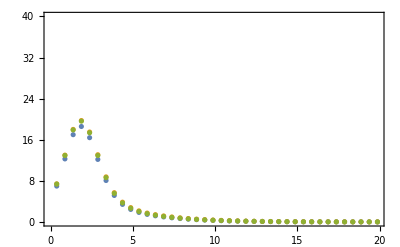
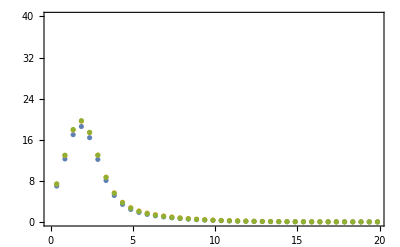
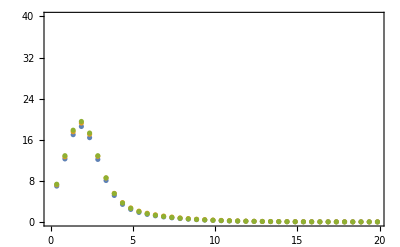
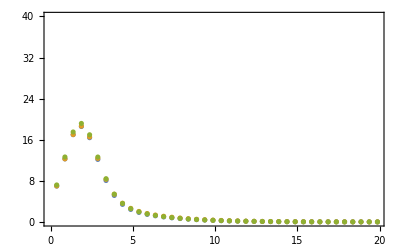
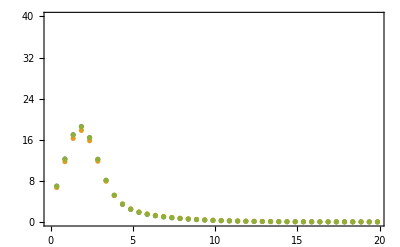

0.03

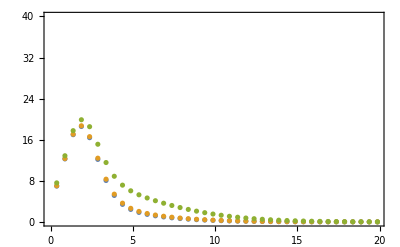
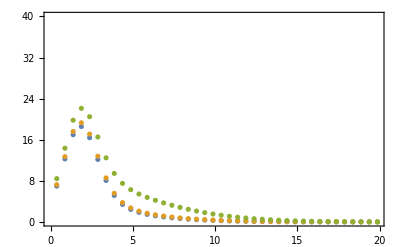
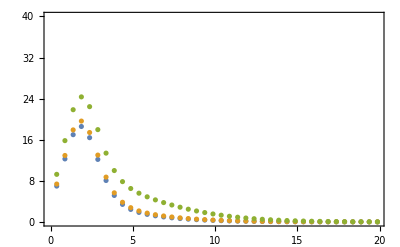
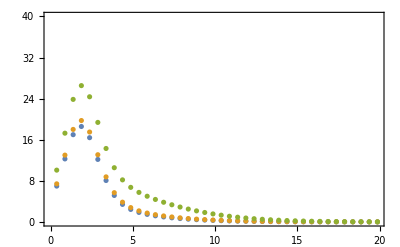
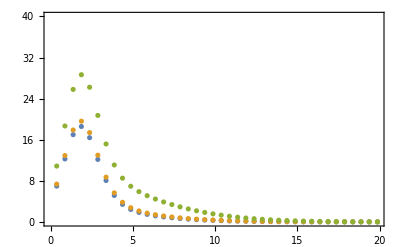
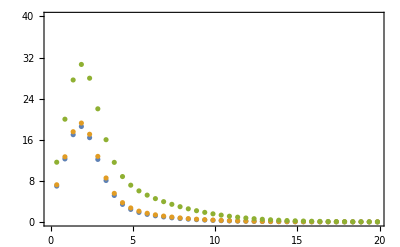
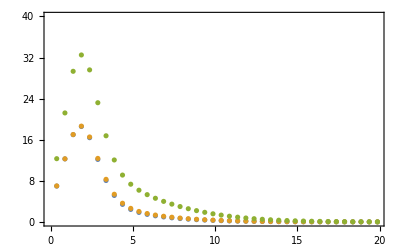
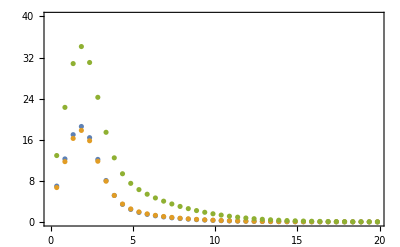

-0.003

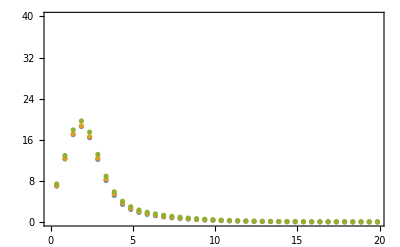
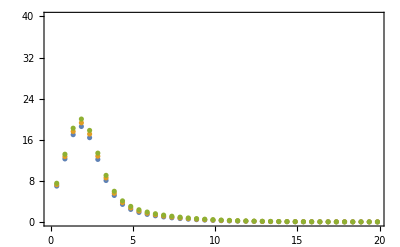
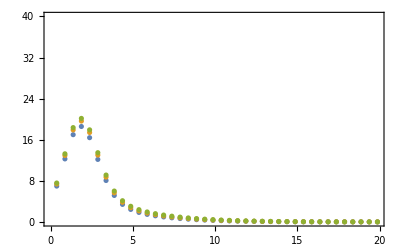
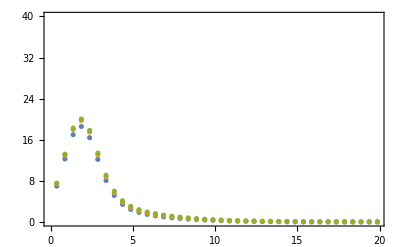
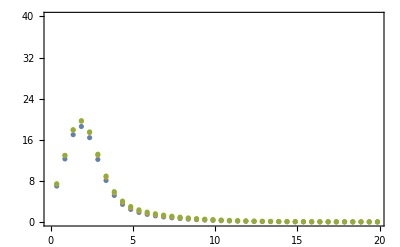
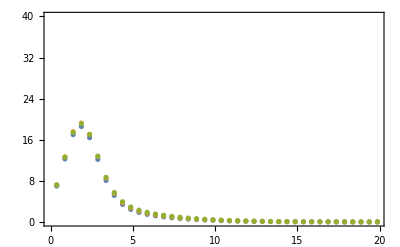
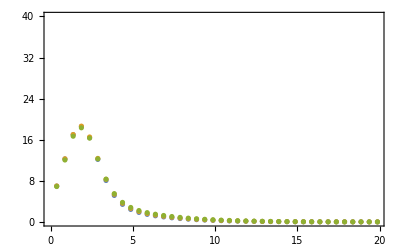
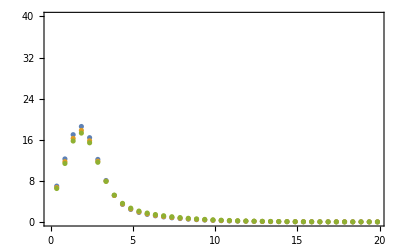

```mathematica
Print[nsi]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSI[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
Print[nsi2]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSI2[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
Print[-nsi]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSIp[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
```

```mathematica
(* checking if it is needed to integrate probability over bin *)
```

```mathematica
Table[{NIntegrate[ratioGen[(Sqrt@0.582)-.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}],ratioGen[(Sqrt@0.582)-.1,delta,0,.5*i]//Chop,ratioGen[(Sqrt@0.582)-.1,delta,0,.5*i]/NIntegrate[ratioGen[(Sqrt@0.582)-.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratioGen[(Sqrt@0.582)+.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}],ratioGen[(Sqrt@0.582)+.1,delta,0,.5*i]//Chop,ratioGen[(Sqrt@0.582)+.1,delta,0,.5*i]/NIntegrate[ratioGen[(Sqrt@0.582)+.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
```

{{0.877206,0.962429,1.09715},{1.02851,1.03866,1.00988},{1.20426,0.84678,0.703154},{0.916722,0.953288,1.03989},{0.970634,0.984752,1.01455},{0.995329,1.00489,1.00961},{1.01309,1.02082,1.00763},{1.02787,1.03465,1.0066},{1.04103,1.04724,1.00597},{1.0532,1.05905,1.00555},{1.06471,1.0703,1.00525},{1.07576,1.08117,1.00502},{1.08647,1.09174,1.00485},{1.09693,1.10208,1.0047},{1.10718,1.11226,1.00458},{1.11728,1.12229,1.00448},{1.12725,1.1322,1.00439},{1.13712,1.14202,1.00431},{1.1469,1.15176,1.00424},{1.1566,1.16144,1.00418},{1.16625,1.17105,1.00412},{1.17584,1.18062,1.00407},{1.18539,1.19015,1.00402},{1.19489,1.19963,1.00397},{1.20436,1.20909,1.00392},{1.21381,1.21852,1.00388},{1.22322,1.22792,1.00384},{1.23261,1.2373,1.0038},{1.24198,1.24666,1.00377},{1.25133,1.256,1.00373},{1.26066,1.26532,1.0037},{1.26998,1.27463,1.00366},{1.27928,1.28393,1.00363},{1.28857,1.29321,1.0036},{1.29785,1.30248,1.00357},{1.30711,1.31174,1.00354},{1.31637,1.321,1.00351},{1.32562,1.33024,1.00349},{1.33486,1.33948,1.00346},{1.34409,1.34871,1.00343}}

{{0.655419,0.748632,1.14222},{0.810253,0.818672,1.01039},{0.967969,0.646053,0.667431},{0.708962,0.741793,1.04631},{0.757298,0.769893,1.01663},{0.779296,0.787785,1.01089},{0.795048,0.801892,1.00861},{0.808115,0.814106,1.00741},{0.819732,0.825215,1.00669},{0.830462,0.835613,1.0062},{0.840604,0.845526,1.00586},{0.850332,0.855088,1.00559},{0.859758,0.86439,1.00539},{0.868956,0.873492,1.00522},{0.877976,0.882437,1.00508},{0.886856,0.891257,1.00496},{0.895623,0.899974,1.00486},{0.904297,0.908607,1.00477},{0.912894,0.91717,1.00468},{0.921426,0.925674,1.00461},{0.929904,0.934126,1.00454},{0.938334,0.942536,1.00448},{0.946725,0.950907,1.00442},{0.95508,0.959246,1.00436},{0.963404,0.967557,1.00431},{0.971701,0.975841,1.00426},{0.979974,0.984104,1.00421},{0.988226,0.992346,1.00417},{0.99646,1.00057,1.00413},{1.00468,1.00878,1.00408},{1.01288,1.01697,1.00404},{1.02106,1.02515,1.004},{1.02924,1.03332,1.00397},{1.0374,1.04148,1.00393},{1.04555,1.04963,1.0039},{1.0537,1.05777,1.00386},{1.06183,1.0659,1.00383},{1.06996,1.07402,1.0038},{1.07808,1.08213,1.00376},{1.08619,1.09024,1.00373}}

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.12983,0.274922,0.406915,0.454595,0.396747,0.259355,0.119043,0.113756,0.464024,1.51243,3.7985}

InterpolatingFunction[…]

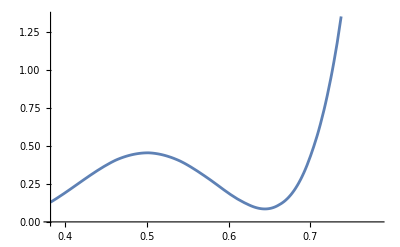

```mathematica
Table[{ls23[[i]],{chis23[[i]]}},{i,Length@ls23}];
Interpolation@%
Plot[%[x],{x,ls23[[1]],ls23[[-1]]}]
```

```mathematica
chiNSI=Table[Sum[dataGenNSI[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSI2=Table[Sum[dataGenNSI2[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI2[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSIp=Table[Sum[dataGenNSIp[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSIp[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSI2p=Table[Sum[dataGenNSI2p[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI2p[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.180407,0.127674,0.0884596,0.062993,0.0514244,0.0538351,0.0702388,0.10058,0.144732,0.202493,0.273623}

{17.9689,19.2235,21.4827,24.8295,29.3268,35.0213,41.9465,50.1245,59.5679,70.2792,82.2497}

{0.362049,0.290227,0.233008,0.190362,0.162256,0.148652,0.149492,0.164699,0.194182,0.237858,0.295727}

{86.4369,77.9054,70.5179,64.2833,59.2028,55.2705,52.4738,50.7969,50.2301,50.794,52.6001}

```mathematica
chis23NSI=Table[Sum[dataGenNSI[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSI2=Table[Sum[dataGenNSI2[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI2[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSIp=Table[Sum[dataGenNSIp[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSIp[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSI2p=Table[Sum[dataGenNSI2p[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI2p[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0469325,0.0318802,0.132583,0.229572,0.257104,0.197775,0.083606,0.00415001,0.124449,0.719661,2.24209}

{20.5254,23.1023,26.5961,30.7736,35.393,40.2096,44.9751,49.4352,53.3247,56.3592,58.2227}

{0.870122,1.10566,1.20738,1.15202,0.961814,0.704091,0.496761,0.520935,1.04433,2.46331,5.38107}

{90.9515,85.2083,79.1027,72.8914,66.8272,61.1598,56.134,51.982,48.9073,47.0543,46.4564}

```mathematica
Join[Table[{ls23[[i]],nsi,{chis23NSI[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],nsi2,{chis23NSI2[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],-nsi,{chis23NSIp[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],-nsi2,{chis23NSI2p[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],nsi*0,{chis23[[i]]}},{i,Length@ls23}]];
func=Interpolation@%
```

InterpolatingFunction[…]

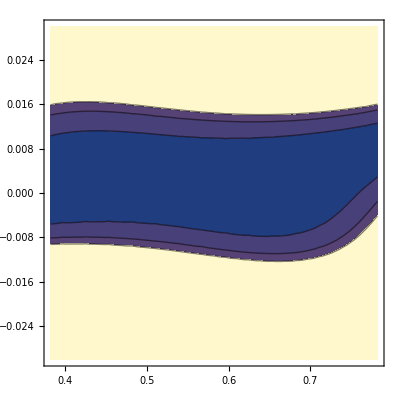

```mathematica
ContourPlot[func[s23,nsii],{s23,ls23[[1]],ls23[[-1]]},{nsii,-.03,.03},Contours->{2.3,4.6,6.}]
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {s23,δ} = {Sqrt@0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(Sqrt@0.582)-.2+passos23*i;
Do[delta=-2.5-1.+passodelta*k;AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

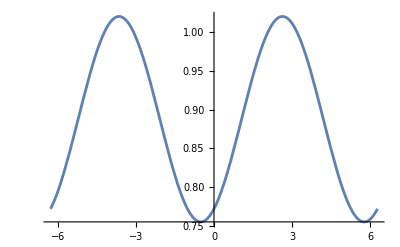

```mathematica
Plot[ratioGen[(Sqrt@0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

```mathematica
ls23d
```

{{0.562889,-3.5},{0.562889,-3.3},{0.562889,-3.1},{0.562889,-2.9},{0.562889,-2.7},{0.562889,-2.5},{0.562889,-2.3},{0.562889,-2.1},{0.562889,-1.9},{0.562889,-1.7},{0.562889,-1.5},{0.602889,-3.5},{0.602889,-3.3},{0.602889,-3.1},{0.602889,-2.9},{0.602889,-2.7},{0.602889,-2.5},{0.602889,-2.3},{0.602889,-2.1},{0.602889,-1.9},{0.602889,-1.7},{0.602889,-1.5},{0.642889,-3.5},{0.642889,-3.3},{0.642889,-3.1},{0.642889,-2.9},{0.642889,-2.7},{0.642889,-2.5},{0.642889,-2.3},{0.642889,-2.1},{0.642889,-1.9},{0.642889,-1.7},{0.642889,-1.5},{0.682889,-3.5},{0.682889,-3.3},{0.682889,-3.1},{0.682889,-2.9},{0.682889,-2.7},{0.682889,-2.5},{0.682889,-2.3},{0.682889,-2.1},{0.682889,-1.9},{0.682889,-1.7},{0.682889,-1.5},{0.722889,-3.5},{0.722889,-3.3},{0.722889,-3.1},{0.722889,-2.9},{0.722889,-2.7},{0.722889,-2.5},{0.722889,-2.3},{0.722889,-2.1},{0.722889,-1.9},{0.722889,-1.7},{0.722889,-1.5},{0.762889,-3.5},{0.762889,-3.3},{0.762889,-3.1},{0.762889,-2.9},{0.762889,-2.7},{0.762889,-2.5},{0.762889,-2.3},{0.762889,-2.1},{0.762889,-1.9},{0.762889,-1.7},{0.762889,-1.5},{0.802889,-3.5},{0.802889,-3.3},{0.802889,-3.1},{0.802889,-2.9},{0.802889,-2.7},{0.802889,-2.5},{0.802889,-2.3},{0.802889,-2.1},{0.802889,-1.9},{0.802889,-1.7},{0.802889,-1.5},{0.842889,-3.5},{0.842889,-3.3},{0.842889,-3.1},{0.842889,-2.9},{0.842889,-2.7},{0.842889,-2.5},{0.842889,-2.3},{0.842889,-2.1},{0.842889,-1.9},{0.842889,-1.7},{0.842889,-1.5},{0.882889,-3.5},{0.882889,-3.3},{0.882889,-3.1},{0.882889,-2.9},{0.882889,-2.7},{0.882889,-2.5},{0.882889,-2.3},{0.882889,-2.1},{0.882889,-1.9},{0.882889,-1.7},{0.882889,-1.5},{0.922889,-3.5},{0.922889,-3.3},{0.922889,-3.1},{0.922889,-2.9},{0.922889,-2.7},{0.922889,-2.5},{0.922889,-2.3},{0.922889,-2.1},{0.922889,-1.9},{0.922889,-1.7},{0.922889,-1.5},{0.962889,-3.5},{0.962889,-3.3},{0.962889,-3.1},{0.962889,-2.9},{0.962889,-2.7},{0.962889,-2.5},{0.962889,-2.3},{0.962889,-2.1},{0.962889,-1.9},{0.962889,-1.7},{0.962889,-1.5}}

```mathematica
dataGen//Dimensions
```

{121,40,2}

54

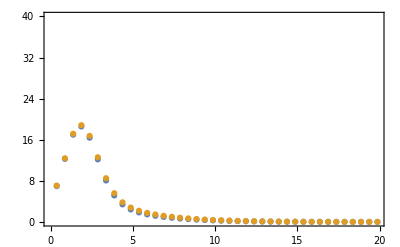

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{1.46026,0.901022,0.542434,0.340553,0.251069,0.236463,0.271114,0.344254,0.460762,0.63985,0.911766,0.57579,0.245967,0.0795708,0.0286563,0.0459637,0.0919952,0.140093,0.179396,0.21565,0.269918,0.375314,0.200626,0.0329024,0.00257221,0.0587087,0.151845,0.240997,0.298721,0.314075,0.293437,0.259229,0.246673,0.0856047,0.00772446,0.0529009,0.168502,0.303796,0.416942,0.480046,0.482112,0.429877,0.346534,0.268502,0.0780945,0.00887756,0.0613382,0.182678,0.322042,0.437505,0.501129,0.501914,0.446629,0.358545,0.274196,0.182515,0.0260575,0.00519212,0.0687802,0.167198,0.259355,0.317752,0.33144,0.306842,0.266477,0.245714,0.681616,0.317658,0.122637,0.0492188,0.0505968,0.0875766,0.13366,0.178003,0.226218,0.299088,0.429292,2.40035,1.66597,1.16095,0.844252,0.673662,0.613076,0.637603,0.73653,0.914095,1.18816,1.58687,7.36617,6.01471,4.99608,4.27804,3.82481,3.6045,3.59439,3.78381,4.17491,4.78124,5.62423,20.8867,18.4703,16.5745,15.1766,14.2479,13.7609,13.6949,14.039,14.7923,15.9627,17.5626,61.6963,57.0327,53.3299,50.5578,48.6825,47.6731,47.5063,48.1687,49.6563,51.9728,55.1248}

InterpolatingFunction[…]

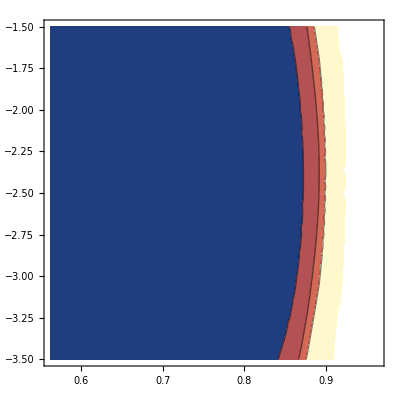

```mathematica
Table[{ls23d[[i]],{chis23d[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```